```mathematica
rateV2[δ_]:=Module[{delta=δ},
(*******************)
(* Free Parameters *)
(*******************)
mx=1 10^3; (* GeV *)
Z=54; (* Atomic Number (Xenon) *)
A=131.904144; (* Atomic Mass (Xenon) *)
a=132;
mN=A 0.93149432; (* Nuclear Mass [GeV] (Xenon) *)


(********************)
(* Fixed Parameters *)
(********************)
mn=0.939;(* Neutron Mass [GeV] *)
rhox=0.3; (* Gev/cm^3 *)
nx=rhox/mx; (* cm^-3 *)
muN=(mx mN)/(mx+mN);(* GeV *)
mun=(mx mn)/(mx+mn);(* GeV *)
Nt=1/mN;(* GeV^-1 *)
fn=1;
fp=1;
alpha=1/137;
alphadark=3.7 10^-2(mx/(10^3(* GeV *)));


(*************************)
(* Velocity Distribution *)
(*************************)
light=2.99792458 10^5;(* km/s *)
v0=220(*km/s*); 
vE=232(*km/s*);
vesc=533(*km/s*); 
vmin[delta_,Er_]:=1/(√(2 Er mN))((Er mN)/muN+delta)light; (* km/s *) (* [delta]=[Er]=GeV *) 
norm=π^(3/2)v0^3(Erf[vesc/v0] -(2 vesc)/(π^(1/2)v0)ⅇ^(-vesc^2/v0^2));  (* (km/s)^3 *)
VelDist[v_,θ_]:=(ⅇ^(-(v^2+vE^2+2 v vE θ)/v0^2))/norm;   (* (km/s)^-3 *)


(****************************)
(* Scattering Cross Section *)
(****************************)
q[Er_]:=√(2 Er  mN);(* GeV *) (* [Er]=GeV *)
b=√(mn^-1 10^3(45 a^(-1/3)-25 a^(-2/3))^-1); (* GeV^-1 *)
u[Er_]:=q[Er]^2 b^2/2; 
c1=-132.841;
c2=38.4859;
c3=-4.08455;
c4=0.153298;
c5=-0.0013897;
F[Er_]:=√(ⅇ^(-u[Er])/a^2(a+c1 u[Er]+c2 u[Er]^2+c3 u[Er]^3+c4 u[Er]^4+c5 u[Er]^5)^2); 
scat[v_,Er_]:=(16 π alpha alphadark  muN^2 Z^2)/((5.06 10^13)^2)1/(v/light)^2 mN/(2 muN^2)F[Er]^2;  (* mV^4/ϵ^2 dσ/dEr GeV^3 cm^2 *) 


(*******************)
(* Scattering Rate *)
(*******************) 
If[delta==300 10^-6,
Er0=Solve[vmin[delta,Er]==vesc+vE,Er][[1]];
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx Nt(10^5)Integrate[v^3 func[v]scat[v,Er],{v,vmin[delta,Er],vesc+vE}];(* s^-1 GeV^-2 cm^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,Er/.Er0 ,500 10^-6}]](* s^-1 GeV^-1 cm^-2 *)
];
](* R/Subscript[σ, 0] s^-1 GeV-1 cm^-2*)
```

```mathematica
(*******************************)
(* Velocity Integral condition *)
(*******************************)
(* delta > ~ 53 10^-6 then vmin never < vesc-vE *)
(* delta < ~ 14 10^-6 then vmin is always < vesc-vE *)
(* 38 ~ < delta < ~ 53 vmin may be larger than vesc+vE *)
par=300 10^-6;
Reduce[vmin[par,Er]< vesc-vE&& 1 10^-6≤ Er≤ 500 10^-6,Er,Reals]
Reduce[vmin[par,Er]> vesc+vE&& 1 10^-6≤ Er≤ 500 10^-6,Er,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.×10^-6≤Er<0.00011522

```mathematica
(*********************)
(* Experimental Data *)
(*********************)
10^3;(* Kg / Tonne*)
1.79 10^-27(* Kg / GeV *);
24 60 60 ;(* s/day *)
const=3.9(* event *)/(47(* tonne - day *)10^3/(1.79 10^-27)(* GeV/tonne *)24 60 60 (* s/day *))(* s^-1 GeV^-1 *)
```

1.71912×10^-36

```mathematica
(******************)
(* epsilon vs mV *)
(******************)
V2rate=rateV2[300 10^-6];
epsilon[mV_]:=√(const/V2rate)mV^2;
```

```mathematica
checkplot={{1.090 10^-1,3.146 10^-7},
{1.225 10^-1,3.971 10^-7},
{1.376 10^-1,5.012 10^-7},
{1.547 10^-1,6.319 10^-7},
{1.738 10^-1,7.958 10^-7},
{1.914 10^-1,9.610 10^-7},
{2.184 10^-1,1.251 10^-6},
{2.465 10^-1,1.615 10^-6},
{2.765 10^-1,1.991 10^-6},
{3.122 10^-1,2.563 10^-6},
{3.497 10^-1,3.230 10^-6},
{3.908 10^-1,4.041 10^-6},
{4.342 10^-1,4.889 10^-6},
{4.877 10^-1,6.258 10^-6},
{5.408 10^-1,7.789 10^-6},
{6.056 10^-1,9.706 10^-6},
{6.508 10^-1,1.117 10^-5},
{7.150 10^-1,1.356 10^-5},
{7.991 10^-1,1.695 10^-5},
{8.851 10^-1,2.100 10^-5},
{1.014 ,2.723 10^-5},
{1.145,3.486 10^-5},
{1.349,4.751 10^-5},
{1.519,6.075 10^-5},
{1.774,8.366 10^-5},
{1.977,1.044 10^-4},
{2.265,1.331 10^-4},
{2.536,1.692 10^-4},
{2.814,2.090 10^-4},
{3.222,2.768 10^-4},
{3.805,3.784 10^-4},
{4.281,4.776 10^-4},
{4.845,6.184 10^-4},
{5.450,7.863 10^-4},
{6.146,9.840 10^-4},
{6.795,1.196 10^-3},
{7.723,1.566 10^-3},
{8.669,1.949 10^-3},
{9.562,2.386 10^-3},
{1.083 10^1,3.079 10^-3},
{1.217 10^1,3.882 10^-3},
{1.367 10^1,4.905 10^-3},
{1.538 10^1,6.239 10^-3},
{1.728 10^1,7.866 10^-3},
{1.942 10^1,9.928 10^-3},
{2.182 10^1,1.250 10^-2},
{2.449 10^1,1.581 10^-2},
{2.740 10^1,1.972 10^-2},
{3.059 10^1,2.475 10^-2},
{3.437 10^1,3.105 10^-2},
{3.841 10^1,3.878 10^-2},
{4.293 10^1,4.853 10^-2},
{4.824 10^1,6.121 10^-2},
{5.237 10^1,7.189 10^-2}};
plotcheck=Interpolation[checkplot]
```

InterpolatingFunction[…]

```mathematica
tPowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

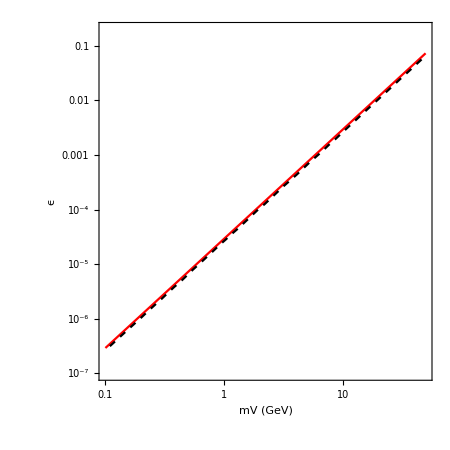

```mathematica
Show[LogLogPlot[epsilon[mv],{mv,0.1,50},PlotStyle->Red,PlotRange->{{0.09999,50},{10^-7,2 10^-1}},FrameTicks-> {{tPowerTicks[True][10^-8, 10^3],Automatic},{tPowerTicks[True][10^-4, 10^3],Automatic}}],LogLogPlot[plotcheck[mv],{mv,1.09 10^-1,5 10^1},PlotStyle->{Black, Dashed}],Frame-> True,AspectRatio->1,FrameLabel-> {"mV (GeV)", "ϵ"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 450]
```

```mathematica
epsilon[1]
```

0.0000291718